```mathematica
(* clear memory *)
ClearAll["Global`*"]
```

```mathematica
(* Declare TDOS function that take the eigenvalue list and Gaussian width as inputs and returns TDOS as a function of energy *)
TDOS[Energy_,Eigenvalues_,Gwidth_]:=Apply[Plus,1/(Sqrt[2Pi]Gwidth)Exp[-(Energy-Eigenvalues)^2/(2 Gwidth^2)]];
```

```mathematica
(* Read orbital eigenvalues, in this example MOs.txt have three columns. If it contains more or less columns, change the size of the array in the second argument *)
Data1=ReadList["/home/zhenzhe/Desktop/mols_MOs/Azulene-4-MOs.txt",{Number,Number,Number,String}];
Data2=ReadList["/home/zhenzhe/Desktop/mols_MOs/Graphene-4-MOs.txt",{Number,Number,Number,String}];
(* Use the second column *)
(*Data1*)
OrbitalEnergies=Data1[[All,3]];
OrbitalEnergies2=Data2[[All,3]];
(*OrbitalEnergiesz*)
Length[OrbitalEnergies]
Length[OrbitalEnergies2]
OrbitalEnergies=OrbitalEnergies*27.2114
OrbitalEnergies2=OrbitalEnergies2*27.2114
```

1758

1763

{663.135,663.134,663.06,663.059,662.908,662.908,662.718,662.717,662.558,661.452,661.452,661.099,661.098,660.48,660.479,660.356,660.235,660.234,659.872,659.872,659.857,659.854,659.725,659.609,659.608,659.443,659.442,658.514,658.055,658.055,657.526,657.526,657.516,657.515,657.502,657.501,656.984,656.984,656.836,656.836,656.77,656.707,656.707,656.125,656.125,655.624,655.624,655.358,655.129,655.129,654.906,654.906,654.757,654.757,653.044,653.044,652.657,652.657,652.587,652.586,651.768,651.768,651.378,650.388,650.388,648.794,648.794,645.962,645.961,642.559,642.558,640.429,139.458,137.329,137.328,137.051,136.396,136.396,135.737,135.737,135.329,135.328,134.373,134.372,134.362,133.32,133.319,132.92,132.92,131.918,131.917,131.189,131.189,127.971,127.971,124.9,124.9,123.877,123.877,122.885,122.885,121.9,121.899,120.931,120.93,119.776,119.776,118.08,117.176,116.059,116.057,115.445,115.445,115.431,115.431,115.022,115.022,113.007,113.007,112.685,112.685,112.355,112.355,111.766,111.765,111.402,109.409,109.409,108.994,108.994,108.611,108.61,107.996,107.374,107.373,106.259,105.722,105.722,105.383,105.383,105.298,105.298,104.906,104.906,102.396,102.396,102.337,102.337,102.1,102.1,102.069,102.006,102.006,101.548,100.983,100.983,100.935,100.935,100.841,100.841,100.642,100.641,99.8784,99.8784,99.6207,99.6198,99.163,98.9831,98.9828,98.6908,98.6906,98.3123,98.3121,98.2361,98.2356,97.7643,97.7643,97.7058,97.7058,97.5164,97.1183,97.118,97.0217,97.0214,96.5006,95.6813,95.6813,95.6538,95.6524,94.9542,94.9539,94.6032,94.6029,94.4246,94.4246,94.3931,94.1563,94.1555,93.8995,93.8995,93.7901,93.7895,93.4886,93.4886,93.4407,93.4401,93.3645,93.3645,93.2401,93.2401,93.118,93.1177,93.0801,92.799,92.7982,92.202,92.2015,91.9952,91.9947,91.9392,90.7198,90.6717,90.6714,90.0504,90.0499,88.43,88.4286,88.3307,88.0814,88.0809,87.9881,87.9875,87.5497,87.3573,87.357,87.1064,87.0974,87.0974,87.0139,87.0136,86.9491,86.9489,86.7962,86.7938,86.6966,86.6966,86.6659,86.6656,86.2199,86.2196,85.8952,85.8724,85.8721,85.7907,85.7905,85.5107,85.5105,85.2484,85.2471,85.2215,84.8498,84.8487,84.7007,84.7004,84.6928,84.6925,84.407,84.407,84.1319,84.13,84.0647,84.0647,83.9439,83.942,83.9134,83.9132,83.3398,83.3398,83.1948,83.1942,83.1556,83.1556,83.1284,83.1281,82.9904,82.954,82.9047,82.9047,82.2263,82.1245,82.1199,82.108,82.108,81.7882,81.6777,81.6772,81.4576,81.4576,81.401,81.3985,81.3286,81.3286,81.2105,81.2094,81.1871,81.1866,81.1583,81.1566,80.7457,80.7457,80.6489,80.647,79.5509,79.5506,79.5052,79.5027,79.4671,79.3544,79.3544,79.266,79.266,78.9082,78.7691,78.7688,78.6325,78.6322,78.2755,78.2744,78.1547,78.1544,78.0418,78.0407,78.0118,77.71,77.7095,77.605,77.6047,77.5879,77.5879,77.5568,77.5566,77.4899,77.4899,77.3541,77.3533,77.3304,77.2445,77.2442,77.2083,77.2083,77.1601,77.1587,77.0777,77.0774,77.0755,77.0352,77.0349,76.9103,76.9103,76.6061,76.4853,76.4847,76.4077,76.4077,76.3919,76.3919,76.0357,76.0349,75.9201,75.9182,75.8872,75.4537,75.4534,75.1084,75.1084,74.9013,74.9007,74.7119,74.7119,74.5552,74.5546,74.4115,74.3807,74.3807,74.1666,74.1663,74.079,73.612,73.4928,73.4928,73.0822,73.0787,72.6161,72.6158,72.4476,72.4474,71.8185,71.8185,71.5954,71.5951,71.4544,71.4544,71.2765,71.0857,71.0808,71.0479,70.914,70.914,70.3741,70.3741,70.2321,70.2321,70.2079,70.2079,70.1638,70.1638,69.9662,69.966,69.8917,69.8117,69.8046,69.8038,69.6721,69.6718,69.6187,69.6185,69.3613,69.3605,68.9156,68.9153,68.7825,68.7825,68.13,68.1286,67.8892,67.8889,67.6541,67.6535,67.6241,67.6236,66.9814,66.6598,66.6598,66.5264,66.4872,66.4867,66.2287,66.0497,66.0494,66.0274,66.0271,65.5128,65.5128,65.3602,65.3599,65.0355,65.0352,64.9999,64.9999,64.9414,64.9411,64.8581,64.8581,64.7838,64.5561,64.5558,63.5601,63.5571,63.2983,63.2981,62.7125,62.7122,62.42,62.4189,62.4061,62.4058,62.1974,62.1732,62.1732,62.0956,62.0956,62.0077,61.7579,61.7579,60.808,60.8077,60.652,60.6267,60.6262,60.4602,60.4594,60.3464,60.3462,60.1279,60.1277,60.1127,60.1124,59.8496,59.8479,59.8436,59.7693,59.769,59.366,59.366,59.3298,59.3296,59.2379,59.2376,59.1657,59.1652,58.6223,58.6221,58.6019,58.6014,58.4457,58.4457,58.2338,58.2329,58.172,58.0596,58.0596,57.8218,57.8218,57.8011,57.8,57.8,57.6071,57.4944,57.4925,57.4509,57.4493,57.3649,57.3646,57.009,57.0014,56.9578,56.9578,56.9488,56.9483,56.4732,56.4193,56.4155,56.2239,56.2237,56.1551,56.1548,56.0473,56.0462,55.963,55.9619,55.8383,55.8381,55.7488,55.6334,55.6332,55.563,55.5619,55.2903,55.1371,55.1368,55.1227,55.1219,54.991,54.9907,54.9295,54.8677,54.8672,54.8672,54.8666,54.7823,54.782,54.5112,54.5096,53.9956,53.9945,53.9662,53.9624,53.8856,53.7316,53.7303,53.7248,53.7246,53.3548,53.3548,53.0911,53.0903,52.9556,52.955,52.8157,52.8157,52.7877,52.6326,52.6312,52.4938,52.4935,52.0225,52.0225,51.8494,51.8478,51.5349,51.5349,51.3653,51.364,51.3153,51.315,51.294,51.2938,51.1131,51.1125,51.0997,51.0995,51.0328,50.8875,50.8872,50.5971,50.494,50.4924,50.4418,50.438,50.1884,50.1068,50.1052,50.0875,50.0875,49.9895,49.9895,49.9169,49.9169,49.8586,49.8586,49.7574,49.66,49.6597,49.5136,49.513,49.3106,49.3103,49.3003,49.3,49.2883,49.2883,49.2466,49.2464,48.9884,48.9884,48.879,48.8785,48.8676,48.867,48.4728,48.1432,48.143,48.1421,48.119,48.1185,48.0893,48.0891,48.0366,48.0363,47.4472,47.4469,47.3952,47.3946,47.2907,47.2901,47.2409,46.9808,46.6515,46.6512,46.5514,46.5007,46.5002,46.365,46.365,46.3274,46.1263,46.1263,46.0444,46.0439,45.7783,45.778,45.7696,45.7682,45.5805,45.5805,45.5007,45.5007,45.4594,45.4591,45.3364,45.3356,45.1881,45.1168,45.1168,45.0721,45.0721,44.8408,44.8408,44.7788,44.76,44.7598,44.7573,44.7573,44.7339,44.7339,44.5271,44.5266,44.2724,44.2716,44.0136,44.0136,43.9037,43.9037,43.7636,43.5913,43.591,43.5562,43.5562,43.3891,42.9812,42.9812,42.935,42.9336,42.7034,42.7031,42.7001,42.6985,42.5379,42.5374,41.8321,41.5265,41.5254,41.4299,41.4299,41.3211,41.3208,41.2612,41.2606,41.2484,41.2481,41.0791,41.0789,40.9779,40.9572,40.9564,40.9251,40.9246,40.0821,40.0818,39.9523,39.9518,39.1665,39.1665,38.8614,38.8601,38.7229,38.7226,38.6103,38.6103,38.3784,38.0258,38.0258,38.0121,38.0121,37.62,37.1681,37.1681,37.0603,37.0597,36.6913,36.691,36.6535,36.525,36.525,36.0766,36.0744,36.0742,35.6045,35.6042,35.2423,35.2423,35.1868,35.1868,34.9713,34.971,34.7895,34.6684,34.6679,34.2036,33.8306,33.8292,33.7966,33.7963,33.7114,33.7111,33.701,33.701,33.6104,33.6102,33.5653,33.5647,33.3889,33.3889,33.2964,33.0651,32.9644,32.9078,32.9076,32.7797,32.7775,32.6665,32.6662,32.5231,32.5228,32.415,32.4148,32.411,32.4107,32.2746,32.2746,32.1252,32.125,32.0817,32.0814,31.965,31.9647,31.9304,31.8583,31.858,31.7663,31.7663,31.6811,31.6801,31.5399,31.5399,31.2485,31.2175,31.2175,31.2049,31.2047,31.1328,31.1326,31.0602,31.0599,31.0218,31.0218,30.9179,30.9173,30.8926,30.8923,30.8907,30.8583,30.8583,30.7818,30.7815,30.6531,30.6528,30.6283,30.2836,30.2836,30.2637,30.2632,30.0433,30.043,29.9924,29.9924,29.901,29.901,29.8256,29.8253,29.603,29.6027,29.5831,29.5831,29.575,29.5742,29.4076,29.4076,29.391,29.391,29.3848,29.3848,29.3772,29.3769,29.3298,29.3162,29.3162,29.3091,29.163,29.163,29.1094,29.1091,29.0052,29.0049,28.9439,28.9434,28.9314,28.8204,28.7235,28.723,28.6713,28.671,28.5752,28.5752,28.4272,28.4272,28.4215,28.4215,28.4035,28.4033,28.3799,28.3799,28.354,28.3535,28.2585,28.0136,28.0136,27.9186,27.9186,27.8661,27.8501,27.8492,27.7948,27.7945,27.671,27.5284,27.5281,27.4797,27.4794,26.9572,26.957,26.9374,26.9366,26.8778,26.8762,26.8449,26.8449,26.6642,26.6642,26.5602,26.5597,26.3134,26.3132,26.2127,26.2078,26.2076,26.0429,26.0424,25.9912,25.9469,25.9466,25.9425,25.9423,25.7779,25.7774,25.29,25.29,25.0331,25.0331,25.0266,25.0263,24.8769,24.6807,24.6805,24.6135,24.6135,24.613,24.6119,24.4353,24.435,24.0176,24.0173,23.8086,23.8086,23.7237,23.6843,23.6843,23.6747,23.6747,23.4565,23.4562,23.2796,23.2723,23.2723,23.2723,23.272,23.1849,23.1847,23.1379,23.1379,23.0761,23.0761,22.9291,22.9291,22.9055,22.9055,22.8521,22.6116,22.6116,22.5874,22.4385,22.4382,22.3223,22.3221,22.2889,22.2889,22.115,22.1147,21.9863,21.9855,21.9259,21.9256,21.9204,21.9201,21.8105,21.8105,21.7106,21.654,21.654,21.638,21.638,21.3585,21.3577,21.2491,21.2491,20.9852,20.9737,20.8809,20.8809,20.8254,20.8254,20.7552,20.7552,20.5092,20.509,20.3639,20.3637,20.3019,20.2747,20.2744,20.1802,20.1802,20.1628,20.1626,20.1476,20.1476,20.1381,20.1378,20.0858,20.0856,20.0017,20.0009,19.8826,19.8826,19.7642,19.7639,19.7171,19.7171,19.6387,19.6387,19.6333,19.6325,19.3756,19.3756,19.3261,19.3261,19.2126,19.2123,19.2118,19.174,19.174,19.1647,19.1634,19.159,19.1587,19.1408,19.14,19.1168,19.0219,18.9691,18.9691,18.8948,18.8948,18.8768,18.8648,18.8646,18.5851,18.5593,18.5593,18.5193,18.5193,18.5081,18.5081,18.4638,18.4259,18.4259,18.3506,18.3506,18.2646,18.1225,18.1225,17.9508,17.95,17.8003,17.7709,17.7709,17.7168,17.7168,17.6918,17.6915,17.6591,17.6591,17.6556,17.6556,17.5413,17.541,17.5301,17.5301,17.3557,17.3557,17.313,17.3122,17.3016,17.1533,17.1522,16.9968,16.9962,16.9701,16.9701,16.9451,16.9451,16.8074,16.8074,16.7603,16.76,16.7551,16.6936,16.6349,16.6346,16.4264,16.4264,16.274,16.2738,16.15,16.15,16.1238,16.1238,15.9374,15.9374,15.8613,15.861,15.781,15.6721,15.6721,14.9508,14.9508,14.8332,14.8329,14.8212,14.7867,14.7864,14.6433,14.6433,14.4808,14.4057,14.4054,14.3429,14.3429,14.2122,14.212,14.1701,14.1698,14.0833,14.0688,14.0688,14.0003,14.0003,13.9388,13.9388,13.5964,13.5964,13.4849,13.419,13.3409,13.3409,13.2764,13.2764,13.0792,13.0786,13.0198,13.0198,13.0196,13.019,13.0144,12.8936,12.8933,12.6723,12.6715,12.5243,12.5243,12.4968,12.4968,12.3836,12.3825,12.2498,12.1393,12.1393,11.9583,11.9578,11.856,11.8557,11.8217,11.8214,11.7953,11.7951,11.7839,11.705,11.705,11.6897,11.6895,11.604,11.6038,11.5297,11.4149,11.4149,11.2555,11.2555,11.115,11.1148,11.0489,11.0408,11.0405,11.0367,10.9972,10.9969,10.9529,10.9529,10.8666,10.8666,10.8402,10.8402,10.6154,10.6152,10.5178,10.5178,10.4979,10.4979,10.4446,10.3953,10.395,10.3637,10.3635,10.3458,10.3458,10.3071,10.3071,10.1232,10.1232,10.1022,10.0533,10.053,10.0426,10.0426,9.96128,9.85162,9.85162,9.84019,9.84019,9.77869,9.77869,9.69624,9.69624,9.56698,9.56698,9.44725,9.44644,9.44208,9.44208,9.13786,9.13786,9.10249,9.10221,9.08398,9.08398,9.06439,9.06439,9.01568,9.01568,8.88262,8.86683,8.86683,8.85568,8.85568,8.85432,8.85405,8.81132,8.81132,8.76262,8.76207,8.67064,8.67064,8.63554,8.48832,8.48805,8.28233,8.28233,8.26356,8.26356,8.16179,8.16097,8.09185,8.09185,8.06818,8.06818,7.90137,7.9011,7.89893,7.89893,7.89539,7.89512,7.89484,7.85076,7.85049,7.82681,7.82654,7.81675,7.7792,7.7792,7.746,7.74573,7.64613,7.64586,7.59606,7.59579,7.57892,7.54164,7.54164,7.49837,7.43688,7.43606,7.31823,7.31388,7.31388,7.27415,7.27388,7.27334,7.27334,7.22735,7.19088,7.19088,7.18218,7.1819,7.16912,7.16912,7.08803,7.08748,7.00367,7.00367,6.87278,6.87278,6.85265,6.85237,6.8151,6.81482,6.71986,6.71986,6.66271,6.66217,6.6472,6.6472,6.5457,6.54543,6.45237,6.45182,6.41999,6.41971,6.39169,6.39169,6.38379,6.38379,6.36203,6.36175,6.32583,6.30896,6.29427,6.294,6.17998,6.17998,6.1593,6.1593,6.13481,6.13481,5.89399,5.89399,5.86814,5.86814,5.86188,5.86188,5.84773,5.78269,5.78269,5.73099,5.73072,5.7016,5.7016,5.568,5.568,5.56119,5.50786,5.50786,5.49425,5.49425,5.47765,5.47738,5.38024,5.38024,5.25017,5.2499,5.24119,5.24119,5.18785,5.18758,5.1005,4.89288,4.89288,4.88635,4.88608,4.86894,4.86894,4.74621,4.74621,4.72934,4.61124,4.61124,4.53668,4.53668,4.46648,4.46621,4.38675,4.38675,4.38512,4.38512,4.35763,4.35736,4.21722,4.21722,4.19164,4.17423,4.05504,4.05504,4.02021,4.02021,3.85613,3.85558,3.8213,3.8213,3.81068,3.81041,3.68252,3.68225,3.65313,3.65313,3.58048,3.58048,3.50918,3.50864,3.4466,3.39816,3.38728,3.34891,3.34891,3.27734,3.27734,3.15298,3.15298,3.1353,3.13503,3.0757,2.98591,2.98591,2.8923,2.8738,2.87352,2.72522,2.72495,2.62427,2.62427,2.34617,2.34617,2.338,2.11215,2.11215,2.07215,2.07215,1.90317,1.90317,1.7486,1.7486,1.71758,1.71731,1.51023,1.51023,1.43622,1.43622,1.33064,1.27186,1.21308,1.21308,1.04519,1.04519,0.936616,0.936616,0.905323,0.768994,0.768994,0.346129,-0.385313,-0.385313,-0.520282,-0.520282,-1.30207,-1.30234,-1.5418,-1.5418,-6.42352,-6.42352,-6.84394,-6.84421,-7.19034,-7.19061,-7.423,-8.29186,-8.29186,-8.43962,-9.00942,-9.00969,-9.72671,-9.72671,-9.77597,-9.77597,-10.1335,-10.1335,-11.2435,-11.2435,-11.2484,-11.2484,-11.2701,-11.2701,-11.3559,-11.3559,-11.3654,-11.3654,-11.4791,-11.4791,-11.5371,-11.5371,-11.5599,-11.5945,-11.7888,-11.7891,-12.074,-12.262,-12.262,-12.3728,-12.373,-12.4454,-12.4454,-12.5798,-12.5798,-12.588,-12.588,-12.8484,-12.8484,-12.9349,-12.9349,-12.9817,-12.9817,-13.0128,-13.0128,-13.0571,-13.1453,-13.1973,-13.1973,-13.3336,-13.3339,-13.3918,-13.3918,-13.6933,-13.6933,-13.6974,-13.6974,-13.766,-13.766,-14.0092,-14.0092,-14.1173,-14.185,-14.185,-14.3246,-14.3252,-14.6256,-14.6259,-14.7203,-14.7203,-14.9546,-15.255,-15.255,-15.5339,-15.5342,-15.8248,-15.8251,-16.0485,-16.0487,-16.0732,-16.1026,-16.1026,-16.1992,-16.1992,-16.4972,-16.6651,-16.6651,-16.701,-16.7013,-16.944,-16.944,-17.3992,-17.3995,-17.476,-17.4762,-17.8523,-17.8523,-18.7579,-18.8316,-18.8319,-18.8472,-18.8472,-19.1386,-19.1389,-19.263,-19.4099,-19.4249,-19.4249,-20.1438,-20.1438,-20.3125,-20.3125,-20.8045,-20.8045,-21.2415,-21.2415,-21.6581,-21.6581,-22.0801,-22.0801,-22.4366,-22.4366,-22.515,-22.8851,-23.2135,-23.2135,-23.3332,-23.3335,-23.8622,-23.8622,-23.8766,-23.8769,-24.133,-24.133,-25.118,-25.118,-25.1471,-25.1474,-25.2326,-25.2329,-25.2827,-25.4576,-25.4579,-26.53,-26.5303,-26.8957,-26.8957,-27.2484,-27.2484,-27.4811,-27.4811,-27.5613,-279.579,-279.579,-279.579,-279.579,-279.579,-279.58,-279.58,-279.58,-279.58,-280.195,-280.195,-280.195,-280.195,-280.195,-280.195,-280.195,-280.195,-280.195,-280.361,-280.361,-280.362,-280.362,-280.362,-280.362,-280.362,-280.362,-280.362,-280.371,-280.371,-280.371,-280.371,-280.372,-280.372,-280.372,-280.372,-280.372,-280.508,-280.508,-280.509,-280.509,-280.509,-280.509,-280.509,-280.509,-280.509,-280.52,-280.52,-280.52,-280.52,-280.52,-280.52,-280.521,-280.521,-280.521,-280.697,-280.697,-280.697,-280.697,-280.697,-280.697,-280.697,-280.697,-280.697,-280.697,-280.698,-280.698,-280.698,-280.698,-280.698,-280.698,-280.698,-280.698}

{663.343,663.342,663.332,663.306,663.283,663.283,661.473,661.472,661.468,661.455,661.454,661.432,661.431,661.426,661.409,661.408,661.385,661.364,660.382,660.177,660.177,659.948,659.947,659.843,659.827,659.788,659.787,659.736,659.736,659.706,657.629,657.55,657.549,657.464,657.463,657.365,657.045,657.042,657.042,656.901,656.901,656.752,655.525,655.27,655.268,654.899,654.899,654.674,654.007,653.962,653.962,653.959,653.739,653.739,653.477,653.468,653.468,653.309,653.308,653.248,651.887,651.759,651.758,650.741,650.741,648.606,648.453,645.773,645.771,642.572,642.571,640.536,138.195,136.166,136.164,135.971,135.928,135.927,135.579,134.915,134.914,134.894,134.892,134.551,134.477,133.687,133.687,133.273,133.218,133.218,133.149,132.504,132.503,127.711,127.709,125.862,123.122,121.966,121.965,120.679,120.501,120.5,119.596,119.38,119.379,119.24,119.239,118.479,118.396,118.055,117.9,117.899,117.69,117.69,117.232,117.232,117.125,117.124,117.039,116.491,114.356,114.085,114.084,113.865,113.864,113.823,107.741,107.74,107.627,107.626,107.461,107.349,106.853,106.443,106.441,106.176,105.764,105.763,104.817,104.816,104.621,104.576,104.575,104.301,104.283,104.258,104.257,103.909,103.909,103.721,102.988,102.988,102.983,102.983,102.549,102.249,101.958,101.958,101.691,101.69,101.641,101.547,101.432,100.359,100.358,100.22,99.8283,99.8275,99.7393,99.7388,99.5733,99.0857,99.0849,98.8606,98.7262,98.6076,98.4917,98.4914,98.259,98.2579,97.3757,97.3744,96.9112,96.8718,96.8712,96.6584,96.1956,95.9147,95.8606,95.8598,95.7351,95.7346,95.38,95.3798,95.3294,95.312,95.3109,95.1253,95.0089,95.0086,94.9346,94.934,94.7847,94.7085,94.4018,94.2388,94.238,93.6902,93.6889,92.5019,92.2317,91.9362,91.9356,91.8175,91.8148,91.8145,91.3402,91.3144,91.3141,91.2923,91.2923,91.1217,90.959,89.9369,89.9367,89.9266,89.9261,89.9255,89.2548,89.2531,89.2392,88.8904,88.8874,88.8319,88.1342,87.8901,87.8898,87.7132,87.6534,87.6525,87.3208,87.3208,87.2248,87.1935,87.1932,86.7774,86.7252,86.2634,86.2634,86.2044,86.074,86.0645,86.0008,85.8795,85.8789,85.8022,85.7932,85.7834,85.0196,84.889,84.7227,84.7221,84.3001,84.2998,84.1692,84.1015,84.0998,83.7997,83.7991,83.6778,83.677,83.6497,83.1472,83.0919,82.9708,82.9703,82.8837,82.7978,82.7975,82.755,82.7499,82.6242,82.4824,82.4824,82.1403,81.9226,81.8157,81.8154,81.576,81.5757,81.4418,81.3019,81.1273,81.1107,81.1104,80.9784,80.9781,80.838,80.8377,80.697,80.3596,80.1455,80.1455,80.0723,80.072,80.0165,80.0154,79.7561,79.7153,79.7128,79.6551,79.6548,79.6197,79.6162,79.5732,79.4249,79.38,79.3797,79.1493,79.149,79.1367,79.1142,79.1139,79.1136,79.1117,79.0516,79.0159,78.7354,78.7014,78.7003,78.6946,78.6943,78.6336,78.5231,78.5231,78.4937,78.4573,78.457,78.349,78.3452,78.1707,77.6943,77.6834,77.6801,77.6801,77.5628,77.562,77.5522,77.5269,77.5269,77.4007,77.2717,77.1889,77.187,77.1264,77.1261,76.8325,76.6678,76.5204,76.4687,76.4643,76.4238,76.316,76.3155,75.9598,75.9598,75.8975,75.895,75.765,75.7609,75.6828,75.4768,75.3307,75.3307,75.1875,75.184,74.9894,74.9704,74.6787,74.5307,74.5067,74.5067,74.3791,74.3791,74.3606,74.3413,74.2044,74.2017,74.003,74.0025,74.0017,74.0006,73.3701,73.3162,73.3157,73.249,73.0188,72.8313,72.8275,72.3801,72.378,72.1494,71.6373,71.6367,71.6275,71.6245,71.6068,71.3733,70.6413,70.105,70.0993,70.0993,69.9466,69.9458,69.9412,69.9409,69.8881,69.7232,69.641,69.6394,68.5964,68.4818,68.4778,68.4778,68.271,68.2696,68.1292,68.1289,68.0612,68.0592,66.9215,66.8628,66.8611,66.8154,66.8146,66.7814,66.7615,66.6336,66.4415,66.441,66.3085,66.3077,66.1294,65.9128,65.8625,65.6617,65.1591,65.072,65.0641,65.0638,64.8137,64.6935,64.6918,64.4399,64.4393,64.3724,64.2755,64.275,64.1756,64.1748,64.1073,64.1068,64.0711,64.0584,64.0581,63.9555,63.9555,63.657,63.4243,63.4243,63.3,63.2118,63.1125,63.1114,62.6303,62.6292,62.3367,61.9974,61.9965,61.9906,61.9876,61.7906,61.7465,61.6882,61.6877,61.6387,61.4763,61.3508,61.3312,61.3312,61.2235,61.2213,61.1032,61.1024,60.5489,60.4196,60.4194,60.3489,60.2357,60.2324,59.6477,59.6455,59.6215,59.6213,59.5116,59.4809,59.1701,59.1696,59.1443,59.144,59.0223,59.0221,58.9576,58.7867,58.7867,58.6754,58.4272,58.4261,58.4049,58.2082,58.1989,58.1157,57.8884,57.6955,57.6773,57.6503,57.5366,57.5208,57.52,57.4044,57.3937,57.3927,57.3548,57.1192,57.1184,56.9004,56.8999,56.7994,56.7973,56.7932,56.7932,56.7641,56.7638,56.7224,56.6011,56.557,56.2247,56.2234,56.2223,56.0792,56.0792,55.8383,55.8381,55.7453,55.48,55.4797,55.2982,55.2968,55.1594,54.8778,54.8764,54.8587,54.8582,54.7896,54.5039,54.5039,54.4704,54.4584,54.4348,54.434,54.4057,54.4038,54.3855,54.124,54.1227,53.9912,53.991,53.9409,53.9384,53.7929,53.7926,53.7744,53.7724,53.7716,53.7278,53.5256,53.4508,53.2075,53.207,53.1874,53.1814,52.7071,52.6785,52.5039,52.4951,52.4941,52.4919,52.4908,52.4502,52.3887,52.2897,52.2892,52.284,52.2813,52.2127,52.2119,51.9874,51.9871,51.8644,51.8641,51.5604,51.5558,51.1621,51.0875,51.0867,50.9732,50.8728,50.8723,50.4137,50.4129,50.3229,50.3223,50.2845,50.1414,49.9569,49.8679,49.6951,49.6818,49.6807,49.6796,49.679,49.6407,49.5786,49.5784,49.3258,49.3253,49.0502,49.0499,48.9547,48.7857,48.7854,48.6333,48.3111,48.3106,48.2899,47.9381,47.937,47.6409,47.3938,47.1652,47.165,47.1086,47.1076,46.8738,46.7427,46.741,46.5968,46.565,46.5124,46.5111,46.4754,46.3225,46.2724,46.2722,46.2071,46.206,46.0934,46.0931,46.0485,45.9296,45.9293,45.8662,45.7002,45.6988,45.5505,45.5211,45.5127,45.5122,45.501,44.9459,44.9459,44.5987,44.5225,44.5222,44.5061,44.5056,44.4934,44.4193,44.3641,44.3636,44.243,44.2427,44.2278,44.2278,44.172,44.0501,44.031,43.6025,43.6022,43.4289,43.388,43.3869,43.3831,43.341,43.323,43.3225,43.2642,43.2386,43.2373,43.2264,43.2261,43.1867,43.1864,43.1069,43.0786,43.0773,42.9698,42.9692,42.9143,42.7962,42.5124,42.3984,42.2759,42.2754,42.2618,42.2615,42.2536,42.2536,42.2468,42.1083,42.108,42.108,42.0291,42.0264,41.9611,41.9597,41.9456,41.9407,41.9388,41.905,41.9031,41.6234,41.622,41.5915,41.5341,41.1379,41.1279,41.127,41.0677,41.0672,40.7346,40.7205,40.7202,40.659,40.5883,40.5877,39.8685,39.7368,39.7363,39.5793,39.3226,39.3221,38.3858,38.1341,38.1335,37.5232,37.5229,37.1895,37.1534,36.6265,36.5414,36.5403,36.5305,36.5283,36.3838,36.383,36.2595,36.2592,35.9215,35.6638,35.3008,35.2992,35.1865,35.1846,34.8809,34.8148,34.457,34.3021,34.2523,34.2523,34.2262,34.226,34.2099,34.1323,34.1321,34.0597,34.0594,34.017,33.9166,33.7571,33.6899,33.6893,33.6847,33.6034,33.6023,33.4368,33.236,33.1293,33.1293,33.0235,33.0232,32.996,32.9957,32.7508,32.7503,32.501,32.3661,32.3658,32.365,32.365,32.2956,32.2956,32.1663,32.0499,31.7941,31.7584,31.6447,31.6444,31.4615,31.4564,31.4564,31.3454,31.3454,31.073,31.0645,31.0643,30.9195,30.9192,30.9135,30.9037,30.8585,30.8569,30.8569,30.8417,30.8414,30.7541,30.7258,30.7034,30.6373,30.6259,30.6253,30.6158,30.6158,30.6153,30.5753,30.575,30.3524,30.3519,30.08,29.9129,29.9127,29.8912,29.8776,29.877,29.8378,29.8378,29.7668,29.7655,29.6389,29.6387,29.4757,29.4585,29.4566,29.4215,29.2414,29.2406,29.2256,29.098,29.0974,29.0275,29.0275,28.9717,28.9467,28.8874,28.8865,28.8493,28.849,28.8414,28.8079,28.6354,28.6351,28.5649,28.5491,28.5486,28.545,28.5126,28.5126,28.2699,28.1752,28.1189,28.1034,28.1026,28.0604,28.0544,28.0536,28.0424,28.0424,27.9763,27.9758,27.9456,27.9401,27.8207,27.8198,27.7145,27.7143,27.7077,27.7075,27.6117,27.6114,27.5706,27.5703,27.5309,27.5064,27.5058,27.4577,27.4568,27.4057,27.366,27.2321,27.2041,27.2041,27.1034,27.0734,27.0473,27.0424,27.0419,26.9828,26.9328,26.9325,26.9295,26.9289,26.6966,26.6571,26.3268,26.3265,26.1608,26.1602,26.1077,25.8165,25.816,25.7945,25.4252,25.4247,25.2974,25.1627,24.7526,24.7286,24.6968,24.6965,24.5792,24.5787,24.3373,24.2524,24.2522,24.1009,24.1006,24.0573,23.7629,23.7117,23.7117,23.623,23.6228,23.5294,23.5292,23.4981,23.4032,23.3784,23.3779,23.3019,23.2521,23.2516,23.2056,23.1637,23.1536,23.1531,23.0619,23.0176,23.017,22.9204,22.9196,22.8543,22.7425,22.7417,22.6451,22.6445,22.6249,22.6244,22.5868,22.5868,22.5267,22.4769,22.4769,22.4753,22.4747,22.4396,22.4374,22.377,22.3136,22.291,22.0644,22.0644,22.0393,22.0382,22.0048,21.8766,21.8761,21.8663,21.866,21.7743,21.7686,21.6701,21.4619,21.4611,21.3201,21.1988,21.1985,20.9637,20.9634,20.9517,20.9514,20.916,20.9158,20.7898,20.6183,20.4673,20.4668,20.3745,20.3743,20.282,20.2717,20.2654,20.2654,20.2551,20.2028,20.2023,20.1911,20.07,20.07,20.0551,19.8521,19.7775,19.7767,19.7642,19.7639,19.6798,19.67,19.67,19.6515,19.6306,19.5473,19.5473,19.5266,19.4175,19.417,19.4167,19.3772,19.2893,19.2695,19.2695,19.2287,19.1827,19.1827,19.0295,18.9881,18.9487,18.7723,18.7715,18.6771,18.6768,18.5451,18.5448,18.5446,18.4697,18.4697,18.4393,18.4393,18.412,18.4118,18.3054,18.3046,18.1919,18.1914,18.1857,18.1854,18.0986,18.098,17.9397,17.9176,17.9173,17.8939,17.8915,17.8482,17.7546,17.7386,17.7228,17.6621,17.6618,17.5326,17.4907,17.4901,17.4724,17.3035,17.3035,17.2572,17.0953,17.095,17.0888,17.0885,17.0289,17.0278,16.9347,16.8953,16.861,16.8602,16.8177,16.8175,16.7132,16.7045,16.7043,16.6422,16.6419,16.597,16.5633,16.5146,16.4961,16.3736,16.3734,16.2754,16.2754,16.2379,16.2379,16.2177,16.1859,16.0583,15.9921,15.9921,15.9832,15.9829,15.8713,15.7864,15.7861,15.6784,15.5709,15.5527,15.5527,15.4653,15.2212,15.2207,15.1957,15.0476,15.0476,15.0191,15.0188,14.8898,14.8713,14.6748,14.6743,14.5766,14.5763,14.5641,14.5635,14.4914,14.2702,14.2699,14.2313,14.0346,13.9956,13.9954,13.8841,13.8838,13.8784,13.8599,13.6506,13.6501,13.6027,13.6022,13.3295,13.3292,13.2958,13.2724,12.9553,12.9551,12.9409,12.8786,12.7722,12.6846,12.551,12.5504,12.5377,12.5374,12.5227,12.3289,12.2236,12.1597,12.1591,11.9319,11.9311,11.8198,11.6544,11.6538,11.5833,11.5828,11.4867,11.4794,11.4794,11.4119,11.4114,11.3452,11.2217,11.2051,11.2046,11.1477,11.078,11.0685,11.0078,11.0076,11.0008,10.9999,10.9256,10.9251,10.8753,10.8296,10.8296,10.7205,10.7202,10.4579,10.4579,10.4247,10.3066,10.2835,10.2769,10.2769,10.2707,10.2707,10.195,10.1798,10.1798,10.0688,10.0688,10.0581,10.0579,10.0236,10.023,9.99339,9.96128,9.92236,9.86821,9.86767,9.86332,9.86304,9.78848,9.76862,9.76808,9.69597,9.66059,9.64045,9.63365,9.63365,9.6176,9.57379,9.57351,9.53542,9.46957,9.44399,9.36181,9.36181,9.30385,9.28045,9.28045,9.23718,9.20725,9.20725,9.11228,9.07963,9.07963,9.06004,9.04534,9.04507,8.92398,8.90765,8.90765,8.89894,8.87826,8.87799,8.86166,8.86139,8.85214,8.85187,8.77432,8.7471,8.73132,8.73132,8.69704,8.69704,8.69459,8.64669,8.59064,8.59064,8.45839,8.45812,8.34955,8.33077,8.33077,8.32914,8.32914,8.27036,8.26982,8.23145,8.23118,8.20424,8.17485,8.15553,8.15526,8.14328,8.14301,8.02274,7.89484,7.73239,7.706,7.69674,7.69674,7.69538,7.69511,7.64559,7.64531,7.64423,7.64395,7.62409,7.62382,7.61266,7.58409,7.52695,7.5264,7.52041,7.47198,7.44368,7.43225,7.38653,7.37701,7.3664,7.3664,7.33891,7.33837,7.30762,7.30626,7.28123,7.19469,7.19442,7.1751,7.17483,7.10054,7.10054,7.02163,6.9683,6.93945,6.82544,6.82544,6.78625,6.78598,6.73537,6.66951,6.66951,6.64992,6.59822,6.59795,6.57672,6.47278,6.38271,6.38189,6.37128,6.33917,6.32311,6.32311,6.18896,6.12801,6.12774,6.09671,6.05807,6.05807,5.95658,5.95658,5.95331,5.95331,5.88011,5.8548,5.82514,5.82487,5.68909,5.68909,5.58106,5.58079,5.49997,5.47194,5.4714,5.44908,5.44908,5.3952,5.39493,5.39112,5.39085,5.33398,5.33398,5.20799,5.20799,5.16119,5.16119,5.06132,5.00499,5.00499,4.97887,4.97642,4.97642,4.97125,4.8986,4.8986,4.85533,4.75764,4.69369,4.65886,4.62022,4.59274,4.59274,4.53587,4.52526,4.4877,4.48444,4.48389,4.45832,4.44825,4.34348,4.34267,4.34267,4.29151,4.19219,4.19219,4.14158,4.1413,4.12824,4.12579,4.07572,4.07545,4.04416,3.93722,3.93695,3.92851,3.92851,3.79218,3.79218,3.78511,3.78483,3.69857,3.6983,3.63354,3.54646,3.54592,3.54048,3.40551,3.40551,3.39898,3.39898,3.31761,3.31761,3.30809,3.2553,3.1821,3.07135,3.03108,3.03108,2.89801,2.84468,2.82863,2.82863,2.74236,2.73964,2.73937,2.72658,2.68631,2.68631,2.56821,2.56821,2.52114,2.4063,2.4063,2.36413,2.35896,2.35868,2.24304,2.24304,2.05528,2.04929,1.76684,1.76684,1.69337,1.69337,1.54724,1.5271,1.5271,1.50806,1.50806,1.36302,1.36302,1.3252,1.29445,1.15159,1.15159,1.12927,1.129,1.05662,1.05662,1.02669,0.800015,0.646815,0.504499,-0.184221,-0.341503,-0.746953,-0.746953,-0.754844,-0.755116,-7.1166,-7.1166,-7.15497,-7.15524,-7.61239,-7.68504,-8.32859,-8.33594,-9.01187,-9.01214,-9.09759,-9.09759,-9.81978,-9.82005,-10.1104,-10.1107,-10.3577,-10.576,-10.822,-10.9286,-10.9289,-11.114,-11.1142,-11.1553,-11.1869,-11.1872,-11.2078,-11.2228,-11.2228,-11.3855,-11.4293,-11.5287,-11.7036,-11.7493,-11.7496,-11.9529,-11.9532,-12.0672,-12.0672,-12.3559,-12.3562,-12.3825,-12.3825,-12.7137,-12.7714,-12.7717,-13.0253,-13.0484,-13.1913,-13.3564,-13.3578,-13.36,-13.4422,-13.4424,-13.4735,-13.4735,-13.6169,-13.6169,-13.6324,-13.7624,-13.763,-13.7913,-13.7916,-14.0267,-14.0272,-14.0582,-14.0585,-14.1483,-14.1809,-14.1809,-14.2509,-14.3282,-14.3282,-14.4054,-14.4506,-14.4718,-14.6631,-14.6631,-14.7159,-14.717,-14.7652,-14.7654,-15.1293,-15.1396,-15.1619,-15.4362,-15.5165,-15.517,-15.5646,-15.9013,-15.9015,-16.0852,-16.0852,-16.2863,-16.2863,-16.8264,-16.8264,-16.8466,-16.922,-16.956,-16.9562,-17.2333,-17.6267,-17.9073,-17.9076,-18.0545,-18.3135,-18.3135,-18.8798,-19.0107,-19.0112,-19.1013,-19.1013,-19.4964,-19.4967,-19.6191,-19.62,-19.6624,-19.7076,-19.8798,-19.888,-20.596,-20.6769,-20.6771,-20.8488,-20.8491,-21.9675,-21.9678,-22.0385,-22.0388,-22.3699,-22.6845,-22.8663,-22.8984,-23.3055,-23.3057,-23.5885,-23.5885,-23.8551,-23.8554,-24.1798,-24.3112,-24.3112,-24.4935,-24.6546,-24.7118,-24.7123,-24.9504,-24.9504,-25.2505,-25.3953,-25.9001,-25.9004,-26.4408,-26.4408,-26.8748,-26.9083,-27.2275,-27.2277,-27.4345,-27.4348,-27.5045,-280.203,-280.203,-280.203,-280.203,-280.203,-280.203,-280.203,-280.203,-280.204,-280.204,-280.204,-280.204,-280.237,-280.237,-280.237,-280.237,-280.237,-280.237,-280.259,-280.259,-280.259,-280.259,-280.259,-280.259,-280.265,-280.265,-280.265,-280.265,-280.265,-280.265,-280.266,-280.266,-280.266,-280.266,-280.266,-280.266,-280.423,-280.424,-280.424,-280.424,-280.424,-280.424,-280.491,-280.491,-280.491,-280.491,-280.491,-280.491,-280.53,-280.53,-280.53,-280.53,-280.531,-280.531,-280.532,-280.532,-280.532,-280.532,-280.532,-280.532,-280.544,-280.544,-280.544,-280.544,-280.545,-280.545,-280.552,-280.552,-280.552,-280.552,-280.553,-280.553}

```mathematica
GaussWidth=0.2;
TDOS1=TDOS[Ex,OrbitalEnergies,GaussWidth];
(* TDOS1 is now a smooth function of Ex *)

TDOS2=TDOS[Ex,OrbitalEnergies2,GaussWidth];
```

General::munfl: Exp[-5.83341×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.83339×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.83212×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

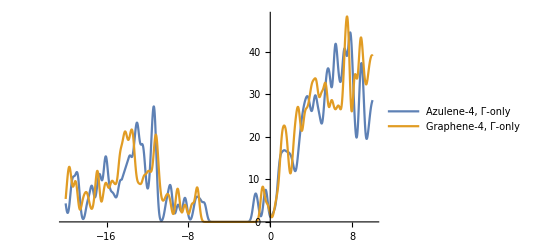

```mathematica
(* Plot two DOS functions. They are the same in this example *)
Emin=-20;
Emax=10;
Plot1=Plot[{TDOS1,TDOS2},{Ex,Emin,Emax},PlotRange->All,PlotLegends->{"Azulene-4, Γ-only","Graphene-4, Γ-only"}]
```